## Pregunta 1

```mathematica
a0 =1/2 Integrate[t^2( UnitStep[t]-UnitStep[t-1] ),{t,0,2}]
```

1/6

```mathematica
an =Simplify[2/2 Integrate[t^2( UnitStep[t]-UnitStep[t-1] )Cos[n Pi t],{t,0,2}],Element[n,Integers]]
```

(2 (-1)^n)/(n^2 π^2)

```mathematica
bn=Simplify[2/2 Integrate[t^2( UnitStep[t]-UnitStep[t-1] )Sin[n Pi t],{t,0,2}],Element[n,Integers]]
```

-(2-2 (-1)^n+(-1)^n n^2 π^2)/(n^3 π^3)

```mathematica
plot1a = Plot[t^2( UnitStep[t]-UnitStep[t-1] ),{t,-4,4},PlotRange->All,PlotStyle->{Orange,Thickness[0.007]}];
plot1b = Plot[1/6+Sum[(2(-1)^n)/(Pi^2 n^2)Cos[n Pi t]+((2/(n^3 Pi^3)-1/(n Pi))(-1)^n- 2/(n^3 Pi^3))Sin[n Pi t],{n,1,200}],{t,-4,4},PlotStyle->{Blue,Thickness[0.01]}];
```

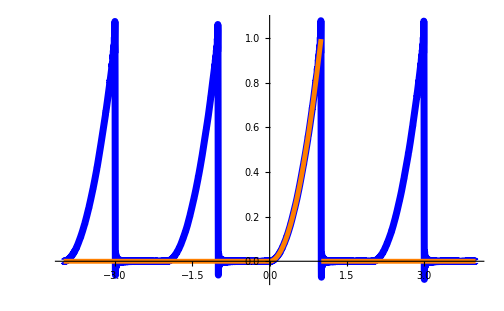

```mathematica
Show[plot1b,plot1a]
```

### (1.b)

```mathematica
Sum[(-1)^n/n^2,{n,1,Infinity}]
```

-π^2/12

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

## Pregunta 2

```mathematica
FourierTransform[Exp[t^2]Sin[t],t,w,FourierParameters->{1, -1}]
```

1/2 √π (Cosh[1/4 (-1+w)^2]+Sinh[1/4 (-1+w)^2]) (-1+Cosh[w]+Sinh[w])

```mathematica
plot2a1 = Plot[1/2 √π (Cosh[1/4 (-1+w)^2]+Sinh[1/4 (-1+w)^2]) (-1+Cosh[w]+Sinh[w]),{w,-5,5},PlotStyle->{Blue,Thickness[0.018]}];
plot2a2 =Plot[(-Exp[1/4] √Pi)/2( Exp[w^2/4-w/2]- Exp[w^2/4+w/2]),{w,-5,5},PlotStyle->{Orange,Thickness[0.007]}];
```

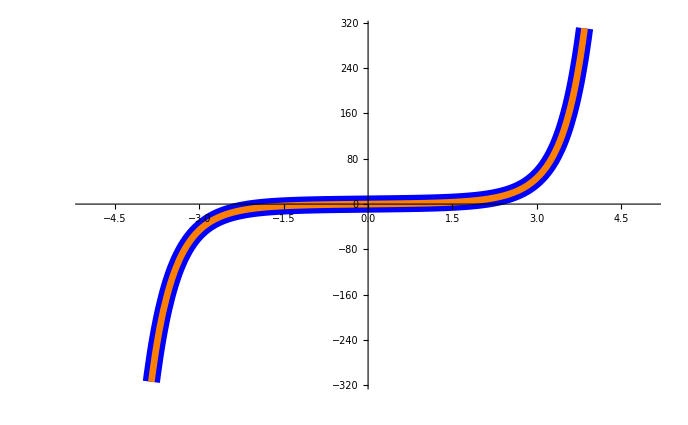

```mathematica
Show[plot2a1,plot2a2](*Vemos que es la misma funcion, tienen el mismo grafico*)
```

### (2.b)

```mathematica
FourierTransform[UnitStep[t- (-a)]-UnitStep[t-a],t,w,FourierParameters->{1, -1}]
```

(2 Sin[a w])/w

### (2.c)

```mathematica
FourierTransform[Sin[t]/t,t,w,FourierParameters->{1, -1}]
```

1/2 π Sign[1-w]+1/2 π Sign[1+w]

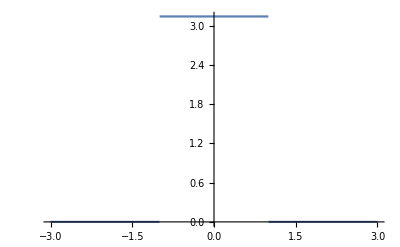

```mathematica
Plot[1/2 π Sign[1-w]+1/2 π Sign[1+w],{w,-3,3}] (*Es la funcion que obtuvumos, pero escrita con la funcion signo*)
```

## Pregunta 3

```mathematica
Clear[a]
```

```mathematica
InverseFourierTransform[(1-w)/(1+2I(w-1)-(w-1)^2),w,t,FourierParameters->{1,-1}]
```

-ⅈ ⅇ^((-1+ⅈ) t) (-1+t) HeavisideTheta[t]

## Pregunta 4

```mathematica
FourierTransform[Exp[-5 t]UnitStep[t],t,w,FourierParameters->{1,-1}]
```

-ⅈ/(-5 ⅈ+w)

```mathematica
Integrate[1/(25+w^2),{w,-Infinity,Infinity}]
```

```mathematica
Integrate[a^2/(25+w^2),{w,-5,-3}]
```

1/20 a^2 (π-4 ArcTan[3/5])

```mathematica
(*Hacemos una comparacion numerica con nuestroa resultados*)
```

```mathematica
N[{1/20 (π-4 ArcTan[3/5]),1/5(ArcTan[1]-ArcTan[3/5])}]
```

{0.0489957,0.0489957}

```mathematica
Integrate[b^2/(25+w^2),{w,2,4}]
```

1/10 b^2 ArcTan[660/989]

```mathematica
N[{1/10  ArcTan[660/989],1/5(ArcTan[4/5]-ArcTan[2/5])}]
```

{0.0588469,0.0588469}

```mathematica
(*Dan lo mismo*)
```